```mathematica
yyyHankRand[x_,y_,t_,k_,w_]=Sum[(BesselJ[0,k √(x^2+(y-d)^2)] Cos[w t]+BesselY[0,k √(x^2+(y-d)^2)] Sin[w t]+BesselJ[0,k √(x^2+(y+d)^2)] Cos[w t]+BesselY[0,k √(x^2+(y+d)^2)] Sin[w t])/(40),{d,10+RandomVariate[UniformDistribution[{-1,1}],20]}];
```

```mathematica
DaForceX[x_,y_,t_,k_,w_] = -D[yyyHankRand[x,y,t,k,w],x];
DaForceY[x_,y_,t_,k_,w_] = -D[yyyHankRand[x,y,t,k,w],y];
CosDisSqWidth = ProbabilityDistribution[(2 Cos[x]^2)/π,{x,-π/2,π/2}]
SincSqWidth[d_] = ProbabilityDistribution[Sinc[x π/(d)]^2/d,{x,-π/2,π/2}]
```

ProbabilityDistribution[(2 Cos[x]^2)/π,{x,-π/2,π/2}]

ProbabilityDistribution[Sinc[(x π)/d]^2/d,{x,-π/2,π/2}]

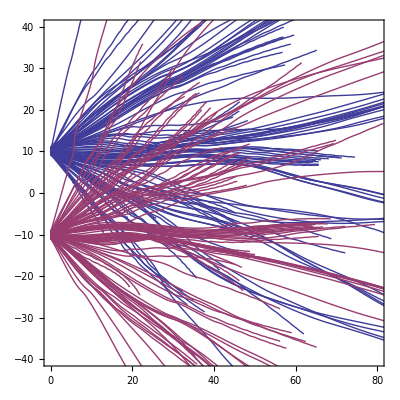

```mathematica
AAA =  1.0;
ddd =10.0;
www = 1.0;
x000 = 0.0;
v000 = 1.0;
kkk= 1.0;
disss = 0.02;
tmax = 60;
xmax = 50;
NMAX=50;
swidth = 1;
phase = 1;

Hollandtabl3DU=Table[NDSolve[{D[x[t],t,t] ==  AAA DaForceX[x[t],y[t],t+phase ,kkk,www]-disss  D[x[t],t], D[y[t],t,t] == AAA DaForceY[x[t],y[t],t+phase ,kkk,www]-disss  D[y[t],t],y[0]== ddd+RandomVariate[UniformDistribution[{-swidth,swidth}]],y'[0]== v000 Sin[RandomVariate[CosDisSqWidth]] ,x[0]== x000,x'[0]==√(1-y'[0]^2)},{x,y},{t,0,tmax}],{NMAX}];
Hollandtabl3DD=Table[NDSolve[{D[x[t],t,t] ==  AAA  DaForceX[x[t],y[t],t+phase ,kkk,www]-disss  D[x[t],t], D[y[t],t,t] == AAA  DaForceY[x[t],y[t],t+phase ,kkk,www]-disss D[y[t],t],y[0]== -ddd+RandomVariate[UniformDistribution[{-swidth,swidth}]],y'[0]== v000 Sin[RandomVariate[CosDisSqWidth]] ,x[0]== x000,x'[0]==√(1-y'[0]^2)},{x,y},{t,0,tmax}],{NMAX}];
ParametricPlot[{{x[t],y[t]}/.Hollandtabl3DU,{x[t],y[t]}/.Hollandtabl3DD},{t,0,tmax},PlotRange->{{0,xmax},{-xmax/2,xmax/2}},Frame->True,Axes->True, AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->14}]
```

```mathematica
AAA =  1.0;
ddd =10.0;
www = 1.0;
x000 = 0.0;
v000 = 1.0;
kkk= 1.0;
disss = 0.02;
tmax = 60;
swidth = 1;
CHUNK = 10;
REPEAT = 100;
CUTTOFF = 40;

outstream=OpenAppend["HydroDoubleSlitPhaseW10P1D2C40.dat"];

Do[

Hollandtabl3DU=Table[NDSolve[{D[x[t],t,t] ==  AAA DaForceX[x[t],y[t],t-1,kkk,www]-disss  D[x[t],t], D[y[t],t,t] == AAA DaForceY[x[t],y[t],t-1,kkk,www]-disss  D[y[t],t],y[0]== ddd+RandomVariate[UniformDistribution[{-swidth,swidth}]],y'[0]== v000 Sin[RandomVariate[CosDisSqWidth]] ,x[0]== x000,x'[0]==√(1-y'[0]^2)},{x,y},{t,0,tmax}]
,{CHUNK}];
Hollandtabl3DD=Table[NDSolve[{D[x[t],t,t] ==  AAA  DaForceX[x[t],y[t],t-1,kkk,www]-disss  D[x[t],t], D[y[t],t,t] == AAA  DaForceY[x[t],y[t],t-1,kkk,www]-disss D[y[t],t],y[0]== -ddd+RandomVariate[UniformDistribution[{-swidth,swidth}]],y'[0]== v000 Sin[RandomVariate[CosDisSqWidth]] ,x[0]== x000,x'[0]==√(1-y'[0]^2)},{x,y},{t,0,tmax}]
,{CHUNK}];


TestTableXU[t_] = Flatten[x[t]/.Hollandtabl3DU];
TestTableYU[t_] = Flatten[y[t]/.Hollandtabl3DU];
TestTableXD[t_] = Flatten[x[t]/.Hollandtabl3DD];
TestTableYD[t_] = Flatten[y[t]/.Hollandtabl3DD];

HistTableAngle = {};
For[NNN = 1,NNN<=Length[TestTableXU[qqq]],NNN++,
For[ttt=1,ttt < tmax, ttt++, If[(TestTableXU[ttt][[NNN]]^2+TestTableYU[ttt][[NNN]]^2)>CUTTOFF^2,AppendTo[HistTableAngle,ArcTan[TestTableYU[ttt][[NNN]]/TestTableXU[ttt][[NNN]]]];Break[]]]
]
For[NNN = 1,NNN<=Length[TestTableXD[qqq]],NNN++,
For[ttt=1,ttt < tmax, ttt++, If[(TestTableXD[ttt][[NNN]]^2+TestTableYD[ttt][[NNN]]^2)>CUTTOFF^2,AppendTo[HistTableAngle,ArcTan[TestTableYD[ttt][[NNN]]/TestTableXD[ttt][[NNN]]]];Break[]]]
];

Export[outstream,HistTableAngle]

WriteString[outstream,"\n"]
,{REPEAT}];

Close[outstream]
```

$Aborted

HydroDoubleSlitPhaseW10P1D2C40.dat

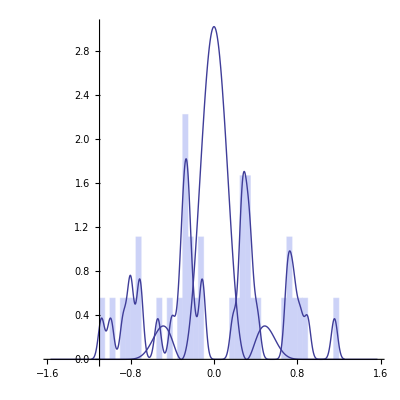

```mathematica
ReadDataSingle = Flatten[Import["HydroDoubleSlitPhaseW10P1D2C40.dat"]];
Show[{Histogram[ReadDataSingle,50,"PDF",PlotRange->{{-π/2,π/2},Full},Axes->{True,False},AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->14}],SmoothHistogram[ReadDataSingle,0.03,PlotStyle->Thick],Plot[2.0(ⅇ^(-Sec[x]^2/0.4^2))/(π Erfc[1/0.4])Cos[5x]^2,{x,-π/2,π/2},PlotRange->{Full,{0,4}}]}]
```

```mathematica
Manipulate[Plot[{yyyHankRand[x,5,t,1,1],yyyHankRand[x,5,t-2.5,1,1]},{x,0,10},PlotRange->{Full,{-0.5,0.5}}],{t,0,10}]
```

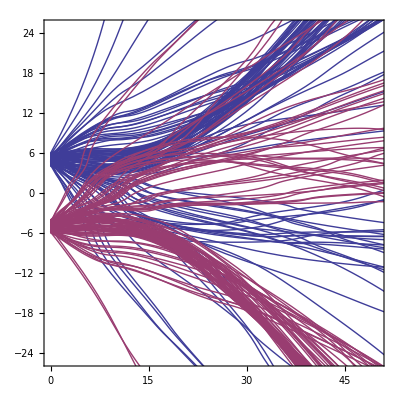

```mathematica
AAA =  1.0;
ddd =5.0;
www = 1.0;
x000 = 0.0;
v000 = 1.0;
kkk= 1.0;
disss = 0.0;
tmax = 80;
xmax = 50;
NMAX=100;
swidth = 1;

Hollandtabl3DU=Table[NDSolve[{D[x[t],t,t] ==  AAA DaForceX[x[t],y[t],t-3,kkk,www]-disss  D[x[t],t], D[y[t],t,t] == AAA DaForceY[x[t],y[t],t-3,kkk,www]-disss  D[y[t],t],y[0]== ddd+RandomVariate[UniformDistribution[{-swidth,swidth}]],y'[0]== v000 Sin[RandomVariate[CosDisSqWidth]] ,x[0]== x000,x'[0]==√(1-y'[0]^2)},{x,y},{t,0,tmax}],{NMAX}];
Hollandtabl3DD=Table[NDSolve[{D[x[t],t,t] ==  AAA  DaForceX[x[t],y[t],t-3,kkk,www]-disss  D[x[t],t], D[y[t],t,t] == AAA  DaForceY[x[t],y[t],t-3,kkk,www]-disss D[y[t],t],y[0]== -ddd+RandomVariate[UniformDistribution[{-swidth,swidth}]],y'[0]== v000 Sin[RandomVariate[CosDisSqWidth]] ,x[0]== x000,x'[0]==√(1-y'[0]^2)},{x,y},{t,0,tmax}],{NMAX}];
ParametricPlot[{{x[t],y[t]}/.Hollandtabl3DU,{x[t],y[t]}/.Hollandtabl3DD},{t,0,tmax},PlotRange->{{0,xmax},{-xmax/2,xmax/2}},Frame->True,Axes->True, AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->14}]
```